```mathematica
$Assumptions={_∈Reals,-1<v<1,-L<z<L};
```

```mathematica
Z={xp,yp,zp}
```

{xp,yp,zp}

```mathematica
X={x,y,z};
```

```mathematica
Pos={t,X-Z}//Flatten
```

{t,x-xp,y-yp,z-zp}

```mathematica
B[V_]:=
Module[{mat},
v=Sqrt[V[[1]]^2+V[[2]]^2+V[[3]]^2];
g=1/Sqrt[1-v^2];
mat={{g,-g V[[1]],-g V[[2]],-g V[[3]]},{-g V[[1]], 1+(g-1)V[[1]]^2/v^2,(g-1)V[[1]] V[[2]]/v^2,(g-1)V[[1]] V[[3]]/v^2},{-g V[[2]], (g-1)(V[[1]]V[[2]])/v^2,1+(g-1)V[[2]]^2/v^2,(g-1)V[[2]] V[[3]]/v^2},{-g V[[3]], (g-1)(V[[1]]V[[3]])/v^2,(g-1)(V[[2]]V[[3]])/v^2,1+(g-1)V[[3]]^2/v^2}}
]
```

```mathematica
V={vx,vy,vz};
```

```mathematica
Phif0[X_,t_]=1/Norm[X];
```

```mathematica
posprime=B[V].Pos;
```

```mathematica
(Xprime=posprime[[2;;]])//MatrixForm;
tprime=posprime[[1]];
```

```mathematica
Phifzv=1/Norm[Xprime]//Simplify;
Pifzv=D[Phifzv,t]//Simplify;
Psifxzv=D[Phifzv,x]//Simplify;
Psifyzv=D[Phifzv,y]//Simplify;
Psifzzv=D[Phifzv,z]//Simplify;
```

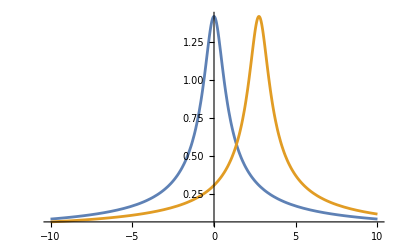

```mathematica
Plot[{Phifzv/.{t->0,y->5/10,z->5/10,
xp->0,yp->0,zp->0,
vx->5/10,vy->0,vz->0},Phifzv/.{t->5.5,y->5/10,z->5/10,
xp->0,yp->0,zp->0,
vx->5/10,vy->0,vz->0}},{x,-10,10},PlotRange->All]
```

```mathematica
Φ=Phifzv/.t->0//Simplify;
Π=Pifzv/.t->0//Simplify;
Ψx=Psifxzv/.t->0//Simplify;
Ψy=Psifyzv/.t->0//Simplify;
Ψz=Psifzzv/.t->0//Simplify;
```

```mathematica
-D[Pifzv,t]+D[Psifxzv,x]+D[Psifyzv,y]+D[Psifzzv,z]//Simplify
```

0

```mathematica
-vx D[Π,xp]-vy D[Π,yp]-vz D[Π,zp]+D[Ψx,x]+D[Ψy,y]+D[Ψz,z]//Simplify
```

0

```mathematica
D[Π,x]-vx D[Ψx,xp]-vy D[Ψx,yp]-vz D[Ψx,zp]//Simplify
```

0

```mathematica
(*DΠdvx=D[Π,vx]//FullSimplify;
DΠdvy=D[Π,vy]//FullSimplify;
DΠdvz=D[Π,vz]//FullSimplify;*)
```

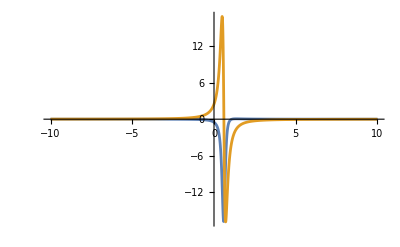

```mathematica
Plot[{Π/.{y->5/10,z->5/10,
xp->6/10,yp->6/10,zp->6/10,
vx->1/10,vy->2/10,vz->3/10},Ψx/.{y->5/10,z->5/10,xp->6/10,yp->6/10,zp->6/10,
vx->1/10,vy->2/10,vz->3/10}},{x,-10,10},PlotRange->All]
```

```mathematica
DΠdvy=((-1+vx^2+vy^2+vz^2) (-y+yp)+2 vy (vx (x-xp)+vy (y-yp)+vz (z-zp))-(3 (vx (x-xp)+vy (y-yp)+vz (z-zp))^2 (vx vy (-x+xp)-y+vx^2 (y-yp)+yp+vz (vz (y-yp)+vy (-z+zp))))/((-1+vy^2+vz^2) x^2+(-1+vy^2+vz^2) xp^2-y^2+vx^2 y^2+vz^2 y^2+2 y yp-2 vx^2 y yp-2 vz^2 y yp-yp^2+vx^2 yp^2+vz^2 yp^2-2 vy vz y z+2 vy vz yp z-z^2+vx^2 z^2+vy^2 z^2+2 vx xp (vy (y-yp)+vz (z-zp))-2 x ((-1+vy^2+vz^2) xp+vx vy (y-yp)+vx vz (z-zp))-2 (vy vz (-y+yp)+(-1+vx^2+vy^2) z) zp+(-1+vx^2+vy^2) zp^2))/((-1+vx^2+vy^2+vz^2)^2 (1/(-1+vx^2+vy^2+vz^2)((-1+vy^2+vz^2) x^2+(-1+vy^2+vz^2) xp^2-y^2+vx^2 y^2+vz^2 y^2+2 y yp-2 vx^2 y yp-2 vz^2 y yp-yp^2+vx^2 yp^2+vz^2 yp^2-2 vy vz y z+2 vy vz yp z-z^2+vx^2 z^2+vy^2 z^2+2 vx xp (vy (y-yp)+vz (z-zp))-2 x ((-1+vy^2+vz^2) xp+vx vy (y-yp)+vx vz (z-zp))-2 (vy vz (-y+yp)+(-1+vx^2+vy^2) z) zp+(-1+vx^2+vy^2) zp^2))^(3/2));
```

```mathematica
DΠdvx=((-1+vx^2+vy^2+vz^2) (-x+xp)+2 vx (vx (x-xp)+vy (y-yp)+vz (z-zp))+(3 (vx (x-xp)+vy (y-yp)+vz (z-zp))^2 (-((-1+vy^2+vz^2) x)+(-1+vy^2+vz^2) xp+vx (vy y-vy yp+vz z-vz zp)))/((-1+vy^2+vz^2) x^2+(-1+vy^2+vz^2) xp^2-y^2+vx^2 y^2+vz^2 y^2+2 y yp-2 vx^2 y yp-2 vz^2 y yp-yp^2+vx^2 yp^2+vz^2 yp^2-2 vy vz y z+2 vy vz yp z-z^2+vx^2 z^2+vy^2 z^2+2 vx xp (vy (y-yp)+vz (z-zp))-2 x ((-1+vy^2+vz^2) xp+vx vy (y-yp)+vx vz (z-zp))-2 (vy vz (-y+yp)+(-1+vx^2+vy^2) z) zp+(-1+vx^2+vy^2) zp^2))/((-1+vx^2+vy^2+vz^2)^2 (1/(-1+vx^2+vy^2+vz^2)((-1+vy^2+vz^2) x^2+(-1+vy^2+vz^2) xp^2-y^2+vx^2 y^2+vz^2 y^2+2 y yp-2 vx^2 y yp-2 vz^2 y yp-yp^2+vx^2 yp^2+vz^2 yp^2-2 vy vz y z+2 vy vz yp z-z^2+vx^2 z^2+vy^2 z^2+2 vx xp (vy (y-yp)+vz (z-zp))-2 x ((-1+vy^2+vz^2) xp+vx vy (y-yp)+vx vz (z-zp))-2 (vy vz (-y+yp)+(-1+vx^2+vy^2) z) zp+(-1+vx^2+vy^2) zp^2))^(3/2));
```

```mathematica
DΠdvz=(2 vz (vx (x-xp)+vy (y-yp)+vz (z-zp))+(-1+vx^2+vy^2+vz^2) (-z+zp)-(3 (vx (x-xp)+vy (y-yp)+vz (z-zp))^2 (vx vz (-x+xp)+vy vz (-y+yp)-z+vx^2 (z-zp)+vy^2 (z-zp)+zp))/((-1+vy^2+vz^2) x^2+(-1+vy^2+vz^2) xp^2-y^2+vx^2 y^2+vz^2 y^2+2 y yp-2 vx^2 y yp-2 vz^2 y yp-yp^2+vx^2 yp^2+vz^2 yp^2-2 vy vz y z+2 vy vz yp z-z^2+vx^2 z^2+vy^2 z^2+2 vx xp (vy (y-yp)+vz (z-zp))-2 x ((-1+vy^2+vz^2) xp+vx vy (y-yp)+vx vz (z-zp))-2 (vy vz (-y+yp)+(-1+vx^2+vy^2) z) zp+(-1+vx^2+vy^2) zp^2))/((-1+vx^2+vy^2+vz^2)^2 (1/(-1+vx^2+vy^2+vz^2)((-1+vy^2+vz^2) x^2+(-1+vy^2+vz^2) xp^2-y^2+vx^2 y^2+vz^2 y^2+2 y yp-2 vx^2 y yp-2 vz^2 y yp-yp^2+vx^2 yp^2+vz^2 yp^2-2 vy vz y z+2 vy vz yp z-z^2+vx^2 z^2+vy^2 z^2+2 vx xp (vy (y-yp)+vz (z-zp))-2 x ((-1+vy^2+vz^2) xp+vx vy (y-yp)+vx vz (z-zp))-2 (vy vz (-y+yp)+(-1+vx^2+vy^2) z) zp+(-1+vx^2+vy^2) zp^2))^(3/2));
```

```mathematica
(*DΠdvy2=D[Π,vy]//FullSimplify;
DΠdvx2=D[Π,vx]//FullSimplify;
DΠdvz2=D[Π,vz]//FullSimplify;*)
DΠdvx/.{x->x,y->y,z->z,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10}//Simplify
```

(25 (483 x^3+43 y^3+41 y^2 z+41 y z^2+43 z^3-47 x^2 (y+z)+x (481 y^2-94 y z+481 z^2)))/(√22 (23 x^2+23 y^2+2 y z+23 z^2+2 x (y+z))^(5/2))

```mathematica
tmp=DΠdvx/.{x->r Sin[th]Cos[ph],y->r Sin[th]Sin[ph],z->r Cos[ph],xp->0,yp->0,zp->0}//Simplify;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in x near {x,y,z} = {6.28921×10^-9,0.344124,0.344124}. NIntegrate obtained 6.44097×10^9 and 1.2001×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in x near {x,y,z} = {-5.80685×10^-11,0.0172062,0.0172062}. NIntegrate obtained -3.22048×10^8 and 6.00049×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in x near {x,y,z} = {1.25784×10^-8,0.688247,0.688247}. NIntegrate obtained 1.28819×10^10 and 2.40019×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

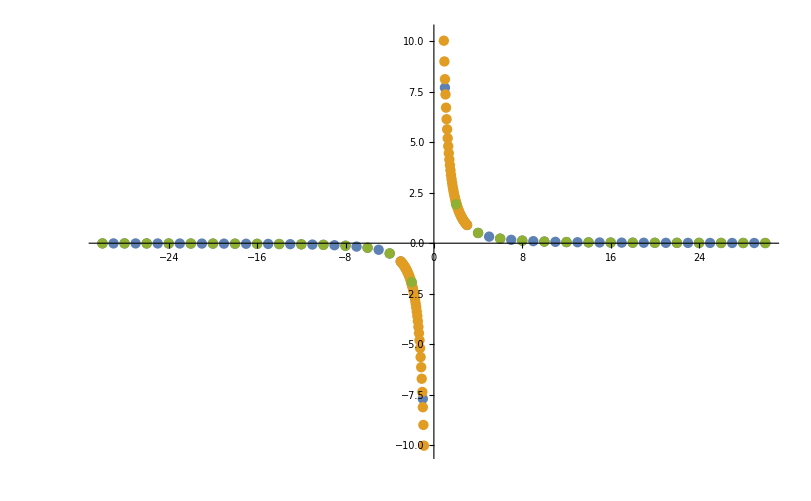

```mathematica
tmp3[N_,h_]:=Table[{i*h,1/h^3 NIntegrate[(25 (483 x^3+43 y^3+41 y^2 z+41 y z^2+43 z^3-47 x^2 (y+z)+x (481 y^2-94 y z+481 z^2)))/(√22 (23 x^2+23 y^2+2 y z+23 z^2+2 x (y+z))^(5/2)),{x,(i-1)*h,(i+1)h},{y,-h,h},{z,-h,h}]},{i,-N,N,2}]
ListPlot[{tmp3[60,0.5],tmp3[120,0.025],tmp3[30,1]}]
```

```mathematica
p1=Plot3D[{DΠdvx/.{x->xx,y->yy,z->0,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10}},{xx,-10,10},{yy,-10,10}]
```

-Graphics3D-

```mathematica
p2=Plot3D[{DΠdvy/.{x->xx,y->yy,z->0,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10}},{xx,-10,10},{yy,-10,10}]
```

-Graphics3D-

```mathematica
p3=Plot3D[{DΠdvz/.{x->xx,y->yy,z->0,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10}},{xx,-10,10},{yy,-10,10}]
```

-Graphics3D-

```mathematica
Plot3D[D[DΠdvy,y]/.{x->xx,y->yy,z->0,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10},{xx,-10,10},{yy,-10,10}]
```

-Graphics3D-

```mathematica
D[DΠdvy,y]/.{x->x,y->0,z->0,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10}//Simplify
```

(135600 √(2/253))/(12167 Abs[x]^3)

```mathematica
DΠdvy/.{x->x,y->0,z->0,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10}//Simplify
```

(1075 x)/(529 √506 Abs[x]^3)